# KREYSZIG

## Chapter 1

### Problems 1.3

#### Problem 35

```mathematica
Manipulate[NIntegrate[Exp[-t^2],{t,0,x}],{x,0,10,0.1}]
```

```mathematica
Manipulate[Sum[((-1)^(n-1)*x^(2*n-1))/((2*n-1)*Factorial[n-1]),{n,1,p}],{p,1,10,1},{x,0,10,0.1}]
```

```mathematica
Manipulate[Plot[{NIntegrate[Exp[-t^2],{t,0,x}],Sum[((-1)^(n-1)*x^(2*n-1))/((2*n-1)*Factorial[n-1]),{n,1,p}]},{x,0,5},PlotLabels->{"Function","McLauren Exapnsion"}],{p,1,35,1}]
```

```mathematica
DSolve[{u'[x]-Exp[-x^2]==0,u[0]==0},u[x],x]
```

{{u[x]→1/2 √π Erf[x]}}

### Problems 1.4

#### Problem 18

{{y→Function[{x},1/(2+Cos[x])]}}

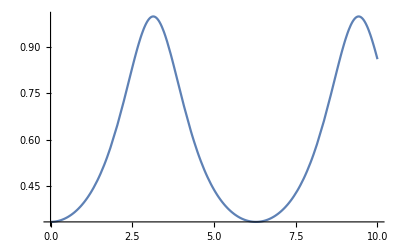

```mathematica
sol=DSolve[{y'[x]-(y[x])^2*Sin[x]==0,y[π/2]==1/2},y,x]
Plot[Evaluate[y[x]/.sol],{x,0,10}]
```

### Problems 1.5

#### Problem 32

```mathematica
ω=π/12
```

π/12

```mathematica
Manipulate[Plot[(c*Subscript[k, 1]*(ω*Sin[ω*t]-(Subscript[k, 1]+Subscript[k, 2])*Cos[ω*t]))/((Subscript[k, 1]+Subscript[k, 2])^2+ω^2)-(P-A*Subscript[k, 1]-T*Subscript[k, 2])/(Subscript[k, 1]+Subscript[k, 2])+k*Exp[(Subscript[k, 1]+Subscript[k, 2])*t],{t,0,100}],{A,60,70,1},{c,0,5,1},{Subscript[k, 1],0.02,1,0.02},{Subscript[k, 2],0.02,1,0.02},{P,0.1,2,0.1},{T,50,80,1},{k,0.02,1,0.02},{ω,π/12,π/12}]
```

#### Problem 34

```mathematica
Manipulate[Plot[Subscript[f, 0]/(Subscript[f, 0]+(1-Subscript[f, 0])*Exp[-k*t]),{t,0,100}],{Subscript[f, 0],0.1,1,0.1},{k,0,1,0.01}]
```

#### Problem 37

```mathematica
Manipulate[Plot[1/(B/(A-H)+(1/Subscript[y, 0]-B/(A-H))*Exp[-(A-H)*t]),{t,0,10}],{A,0.2,2,0.2},{B,0.2,2,0.2},{H,0,0.5,0.1},{Subscript[y, 0],1,10,1}]
```

#### Problem 38

```mathematica
A=1
```

1

```mathematica
B=1
```

1

```mathematica
H=0.2
```

0.2

```mathematica
Subscript[y, 0]=2
```

2

```mathematica
Subscript[y, 1][t_]:=1/(B/(A-H)+(1/Subscript[y, 0]-B/(A-H))*Exp[-(A-H)*t])
```

```mathematica
Subscript[y, 2][t_]:=1/(B/A+(1/(Subscript[y, 1][3])-B/A)*Exp[-(A)*(t-3)])
```

```mathematica
Subscript[y, 3][t_]:=1/(B/(A-H)+(1/(Subscript[y, 2][6])-B/(A-H))*Exp[-(A-H)*(t-6)])
```

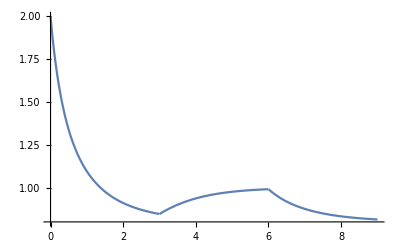

```mathematica
Plot[Piecewise[{{Subscript[y, 1][t],0<t<3},{Subscript[y, 2][t],3<t<6},{Subscript[y, 3][t],6<t<9}}],{t,0,9},PlotRange->{0.8,2}]
```

#### Problem 39

```mathematica
Manipulate[Plot[1/(G+(1/Subscript[y, 0]-G)*Exp[0.1*t]),{t,0,10}],{G,0,0.1,0.005},{Subscript[y, 0],1,100,1}]
```